ⅇ^(-3 N) √(1+ⅇ^(4 N))

Csch[2 η]^3 √(1+Sinh[2 η]^4)

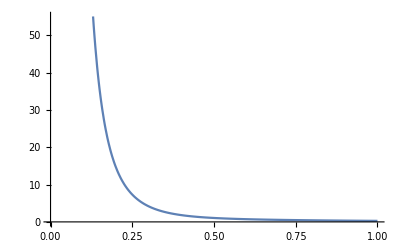

```mathematica
Coth[ArcSinh[Exp[2N]]]/Exp[N]
%/.{N->Log[Sinh[2η]]}
Plot[%,{η,0,1}]
```

```mathematica
D[y[N],{N,1}]+(D[H[N],{N,1}]*D[y[N],{N,1}])/H[N]+D[y[N],{N,2}]==-1.5*(1+D[H[N],{N,1}]/H[N])*y[N]
%/.{H->Function[N,ⅇ^(-3 N) √(1+ⅇ^(4 N))]}//FullSimplify
DSolve[%,y,N]
```

y'[N]+(H'[N] y'[N])/H[N]+y''[N]==-1.5 y[N] (1+H'[N]/H[N])

y''[N]==(3. y[N]+2. y'[N])/(1.+ⅇ^(4 N))

{{y→Function[{N},ⅇ^(3. N) C[1] Hypergeometric2F1[0.75,0.75,2.,-1. ⅇ^(4. N)]+C[2] MeijerG[{{},{1.,1.}},{{-0.25,0.75},{}},-1. ⅇ^(4. N)]]}}

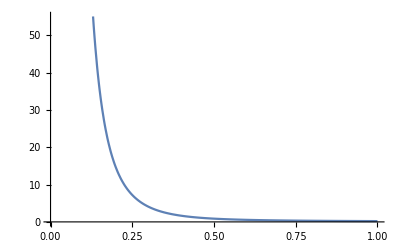

```mathematica
Plot[1/(ⅇ^(3. N) Hypergeometric2F1[0.75,0.75,2.,-1. ⅇ^(4. N)])/.{N->Log[Sinh[2η]]},{η,0,1}]
```

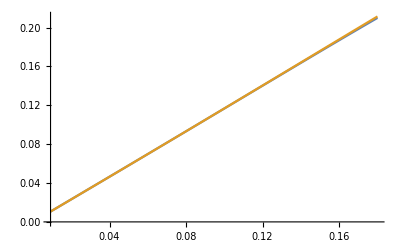

```mathematica
Plot[{Re[1/MeijerG[{{},{1.,1.}},{{-0.25,0.75},{}},-1. ⅇ^(4. N)]]/.{N->Log[Sinh[2η]]},Im[1/MeijerG[{{},{1.,1.}},{{-0.25,0.75},{}},-1. ⅇ^(4. N)]]/.{N->Log[Sinh[2η]]}},{η,0.5*ArcSinh[Exp[-4]],0.5*ArcSinh[Exp[0]]}]
```

```mathematica
DSolve[16*x*(y'[x]+x*y''[x])==(3*y[x]+8*x*y'[x])/(1+x),y[x],x]
```

{{y[x]→x^(3/4) C[1] Hypergeometric2F1[3/4,3/4,2,-x]+C[2] MeijerG[{{},{1,1}},{{-1/4,3/4},{}},-x]}}

```mathematica
Plot[1/Re[MeijerG[{{},{1,1}},{{-1/4,3/4},{}},-x]],{x,0,1}]
```

Plot::pllim: Range specification {{x,0,1}} is not of the form {x, xmin, xmax}.

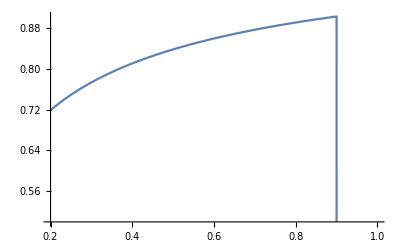

```mathematica
Plot[1/Re[MeijerG[{{},{1,1}},{{-1/4,3/4},{}},-x]],{x,0.2,1}]
```